(0. | 0.0965324
1. | 0.127441
2. | 0.150554
3. | 0.159155
4. | 0.150554
5. | 0.127441
6. | 0.0965324)

InterpolatingFunction[…]

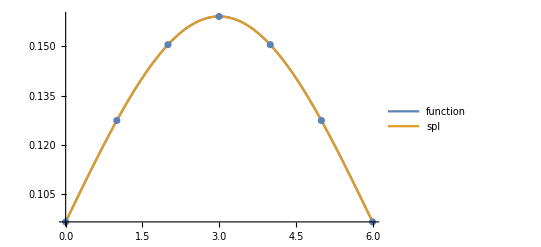

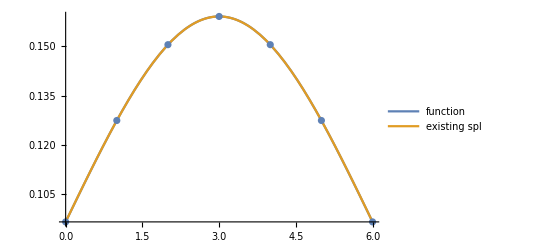

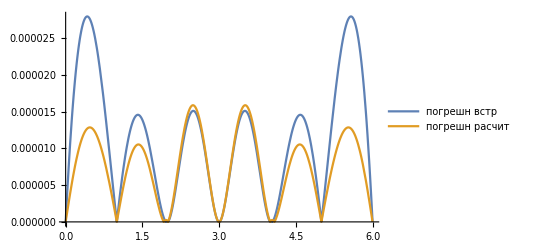

```mathematica
f[x_]:=1/(2π)*ⅇ^(-1/18 x^2+1/3 x-1/2)
xlist={0.,1.,2.,3.,4.,5.,6.};
n:=Length[xlist]-1;
Array[xdata,n+1,0];Array[ydata,n+1,0];
Array[h,n,0];Array[w,n,0];Array[{p,q,r,b},n,1];
For[i=0,i<n+1,i++,xdata[i]=xlist[[i+1]];
ydata[i]=N[f[xdata[i]]]];

For[i=0,i<n+1,i++,h[i]=xdata[i+1]-xdata[i];
w[i]=ydata[i+1]-ydata[i]];
p[1]=0;r[n]=0;
For[i=1,i<n+1,i++,p[i]=h[i-1];
	r[i]=h[i];
	q[i]=N[2*(h[i]+h[i-1])];
	b[i]=N[3*(w[i]/h[i]-w[i-1]/h[i-1])]];
Array[u,n,1];Array[v,n,1];Array[cs,n,0];
u[1]=N[(-r[1])/q[1]];v[1]=N[b[1]/q[1]];
For[i=2,i<n,i++,s=q[i]+p[i]*u[i-1];
	u[i]=N[(-r[i])/s]; v[i]=N[(b[i]-p[i]*v[i-1])/s]];
cs[0]=0;
cs[n]=0;
For[i=n-1,i≥1,i--,cs[i]=u[i]*cs[i+1]+v[i]];
spln[xdata_,ydata_,cs_,n_,x_]:=
	Block[{i=0,h1,a,b,c,d,t},While[x>xdata[i+1],i++];
	h1=xdata[i+1]-xdata[i];
	a=ydata[i];
b=(ydata[i+1]-ydata[i])/h1-(cs[i+1]+2*cs[i])*h1/3;
c=cs[i];
d=(cs[i+1]-cs[i])/(3*h1);
t=x-xdata[i];
Return[a+b*t+c*t*t+d*t*t*t]];
sq[x_]:=spln[xdata,ydata,cs,n,x]
data1=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}];
MatrixForm[data1]
sp=Interpolation[data1,Method->"Spline"]
gr2:=ListPlot[data1]
gr3:=Plot[{f[x],sq[x]},{x,xdata[0],xdata[n]},PlotLegends->{"function", "spl"}];
Show[{gr3,gr2}]
gr4:=Plot[{f[x],sp[x]},{x,xdata[0],xdata[n]},PlotLegends->{"function", "existing spl"}];
Show[{gr4,gr2}]
Plot[{Abs[f[x]-sp[x]],Abs[sq[x]-f[x]]},{x,xdata[0],xdata[n]},PlotLegends->{"погрешн встр", "погрешн расчит"}]
```